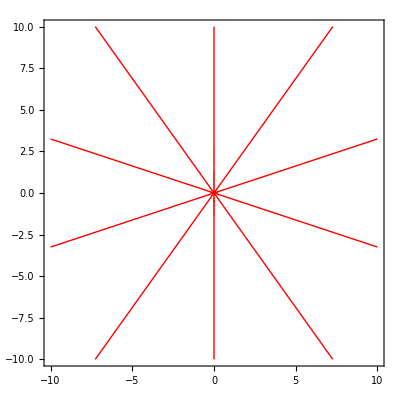

```mathematica
re=ContourPlot[Re[(x+I y)^5]==0,{x,-10,10},{y,-10,10},PlotPoints->100,ContourStyle->{Red,Thick}]
```

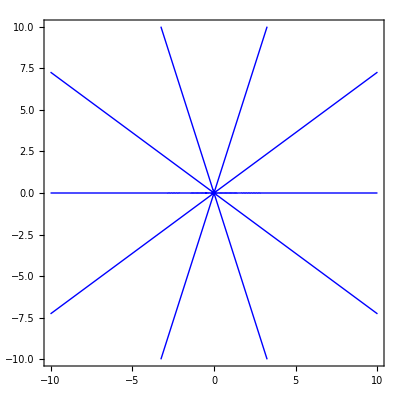

```mathematica
im=ContourPlot[Im[(x+I y)^5]==0,{x,-10,10},{y,-10,10},PlotPoints->100,ContourStyle->{Blue,Thick}]
```

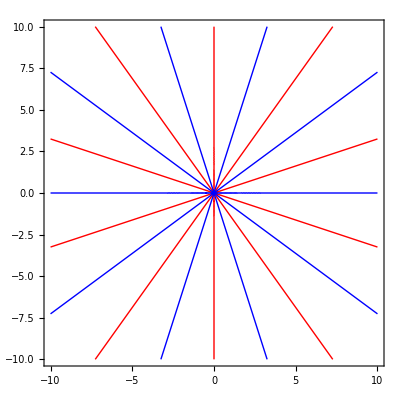

```mathematica
Show[re,im]
```

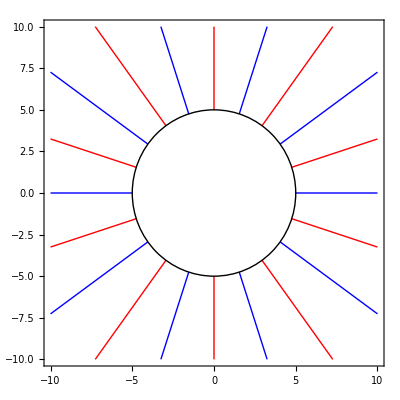

```mathematica
Show[re,im,Graphics[{White,Disk[{0,0},5]}],Graphics[{Thick,Circle[{0,0},5]}]]
```

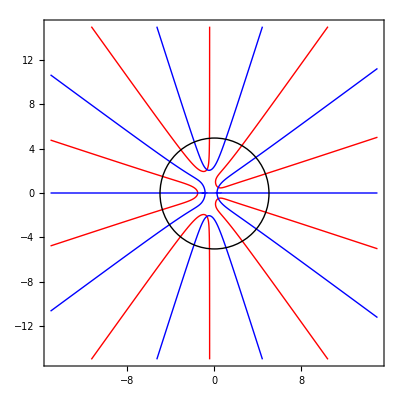

```mathematica
SeedRandom[3]
f[z_]=z^5+RandomInteger[{-5,5}]z^4+RandomInteger[{-5,5}]z^3+RandomInteger[{-5,5}]z^2+RandomInteger[{-5,5}]z+RandomInteger[{-5,5}];
re=ContourPlot[Re[f[x+I y]]==0,{x,-15,15},{y,-15,15},PlotPoints->100,ContourStyle->{Red,Thick}];
im=ContourPlot[Im[f[x+I y]]==0,{x,-15,15},{y,-15,15},PlotPoints->100,ContourStyle->{Blue,Thick}];
Show[re,im,Graphics[{Thick,Circle[{0,0},5]}]]
```